## Principal Component Analysis

We have seen in the lectures how Principal Component Analysis can be used to find the “most important directions” in data. Let’s try it out with a simple 2D dataset that roughly fits on a line:

```mathematica
data=Table[{x,3+2x+RandomVariate[NormalDistribution[0,0.6]]},{x,0,5,0.005}];
```

```mathematica
ListPlot[data]
```

In the video lectures we had the matrix of data with rows corresponding to the variables and columns corresponding to the samples (measurements of those variables). Here, we work with the standard convention in statistics and have rows for samples and columns for variables so we will need to keep in mind this different convention.

The first thing we need to do is subtract the mean in each column (i.e. standardize the data):

```mathematica
standardizedData=Standardize[data,Mean,1&];
```

```mathematica
μ=Mean/@Transpose[data]
```

```mathematica
σ=StandardDeviation/@Transpose[data]
```

```mathematica
ListPlot[standardizedData]
```

Next we compute the singular value decomposition.

```mathematica
{U,Σ,V}=SingularValueDecomposition[standardizedData];
σs=Diagonal[Σ];
```

As expected, we have two singular values, one which is much larger than the other. This reflects the fact that there is much more variance along the line than orthogonal to it.

The singular vectors in the columns of V give us the “most important” directions in the data

```mathematica
Show[ListPlot[standardizedData,AspectRatio->Automatic],Graphics[{Red,Thick,Line[σs[[1]]/(√(Length[data]-1)){{0,0},-V[[All,1]]}]}],Graphics[{Red,Thick,Line[σs[[2]]/(√(Length[data]-1)){{0,0},V[[All,2]]}]}],PlotRange->All]
```

The singular vectors in the columns of U give us the projection of the data long those “most important” directions (i.e. the same as standardizedData.V)

```mathematica
ListPlot[U[[All,1;;2]].Σ[[1;;2,1;;2]]]
```

We can also directly compute this projected form of the data using PrincipalComponents

```mathematica
ListPlot[PrincipalComponents[standardizedData]]
```

### In higher dimensions

Construct a 3-dimensional dataset with 3 variables:

```mathematica
data3D=Table[{x,3+2x+RandomVariate[NormalDistribution[0,0.6]],7+4x+RandomVariate[NormalDistribution[0,6]]},{x,0,5,0.005}];
```

```mathematica
ListPointPlot3D[data3D]
```

-Graphics3D-

In this case we choose to standardise by subtracting the mean and dividing by the standard deviation

```mathematica
standardizedData3D=Standardize[data3D];
```

```mathematica
μ=Mean/@Transpose[data3D]
```

{2.5,7.99469,16.6246}

```mathematica
σ=StandardDeviation/@Transpose[data3D]
```

{1.44554,2.96696,8.24179}

```mathematica
ListPointPlot3D[standardizedData3D]
```

-Graphics3D-

Next we compute the singular value decomposition.

```mathematica
{U,Σ,V}=SingularValueDecomposition[standardizedData3D];
σs=Diagonal[Σ];
```

As expected, we have two singular values, one which is much larger than the other. This reflects the fact that there is much more variance along the line than orthogonal to it.

The singular vectors in the columns of V give us the “most important” directions in the data

```mathematica
Show[ListPointPlot3D[standardizedData3D,BoxRatios->Automatic],Graphics3D[{Red,Thick,Line[σs[[1]]/(√(Length[data]-1)){{0,0,0},-V[[All,1]]}]}],Graphics3D[{Red,Thick,Line[σs[[2]]/(√(Length[data]-1)){{0,0,0},V[[All,2]]}]}],Graphics3D[{Red,Thick,Line[σs[[3]]/(√(Length[data]-1)){{0,0,0},V[[All,3]]}]}],PlotRange->All]
```

-Graphics3D-

The singular vectors in the columns of U give us the projection of the data long those “most important” directions (i.e. the same as standardizedData.V)

```mathematica
ListPointPlot3D[U[[All,1;;3]].Σ[[1;;3,1;;3]]]
```

-Graphics3D-

We can also directly compute this projected form of the data using PrincipalComponents

```mathematica
ListPointPlot3D[PrincipalComponents[standardizedData3D]]
```

-Graphics3D-

## Identifying types of flower

Let’s now use PCA to identify the type of a flower based on measurements of their properties. We will work with a dataset for three different types of iris: setosa, versicolor and virginica.

```mathematica
WolframAlpha["Iris",{{"Image:PlantData",1},"Content"}]
```

The dataset is available directly through Mathematica and contains 4 variables for the length and width of the sepals and petals (in centimeters). Let’s load the data:

```mathematica
iris=ExampleData[{"MachineLearning","FisherIris"}, "Data"];
```

Rearrange the data so that it is grouped by species:

```mathematica
irisbyspecies=GroupBy[iris,Last->First]
```

Let’s first try to plot the data. This is a 4-dimensional dataset (one dimension for each variable) so we don’t have an easy way to visualise it all. Instead,  just visualise three dimensions by dropping one dimension

```mathematica
ListPointPlot3D[irisbyspecies[[All,All,{2,3,4}]]]
```

It looks like there is hope for separating out the species based on their properties, but it is difficult working with 4-dimensional data. Instead, let’s project it onto the two-dimensional space spanned by the first two principal components. We do this as before: standardize the data, use the SVD to find the principal components and the projection of the data onto those components and then un-standardize the result for plotting.  Instead of doing those steps manually again, let’s use Mathematica’s DimensionReduction function which does exactly that. We tell it to use Principal Component Analysis and to project onto two dimensions

```mathematica
diris=DimensionReduction[iris[[All,1]], 2, Method->"PrincipalComponentsAnalysis"]
```

The result is a DimensionReducerFunction which takes in a vector of 4 numbers and returns a vector of two numbers obtained by projecting along the two principal directions. We now apply this projection function to our iris data

```mathematica
dirisbyspecies=diris/@irisbyspecies
```

When we plot this lower dimensional representation of the data, we can clearly delineate between the species:

```mathematica
dirisbyspecies
```

```mathematica
ListPlot[dirisbyspecies]
```

We can go even further than this. We have seen how we can use PCA to project high-dimensional data onto a lower dimensional surface, but we could also reconstruct those projected vectors in the original 4-dimensional space. For example, let’s take one sample of the setosa species:

```mathematica
setosa1=irisbyspecies["setosa"][[1]]
```

We can project this onto the lower-dimensional space:

```mathematica
pcs=diris[setosa1]
```

Then we can take these principal components and combine them with the principal component vectors to reconstruct a 4-vector in the original space. This will be the closest point on our lower-dimensional surface to the original 4-dimensional sample:

```mathematica
diris[pcs,"OriginalData"]
```

We can do these two steps (projection and reconstruction) in one go by asking for the reconstructed vector directly:

```mathematica
diris[setosa1,"ReconstructedVectors"]
```

```mathematica
diris[irisbyspecies["setosa"][[1]],"ReconstructedVectors"]
```

Now let’s do this for all sample points and plot the result:

```mathematica
With[{coords={2,3,4}},Row[{Show[ListPointPlot3D[irisbyspecies[[All,All,coords]],ImageSize->500],Graphics3D[{Opacity[0.3],Gray,InfinitePlane[diris[irisbyspecies["setosa"][[1;;3]],"ReconstructedVectors"][[All,coords]]]}]],Show[ListPointPlot3D[(diris[#,"ReconstructedVectors"]&/@irisbyspecies)[[All,All,coords]],ImageSize->500],Graphics3D[{Opacity[0.3],Gray,InfinitePlane[diris[irisbyspecies["setosa"][[1;;3]],"ReconstructedVectors"][[All,coords]]]}]]}]]
```

Finally, we can also use this approach to fill in missing data. For example, say we had missed a measurement for our first setosa sample

```mathematica
setosa1
```

```mathematica
setosa1missing={5.1,Missing[],1.4,0.2}
```

We can still project this onto the lower dimensional space

```mathematica
diris[setosa1missing]
```

And we can reconstruct a 4-dimensional vector from this, “filling in” the missing  piece:

```mathematica
diris[setosa1missing,"ReconstructedVectors"]
```

If all we want to do is fill in the missing piece and leave the others unchanged, then we could do that too:

```mathematica
diris[setosa1missing,"ImputedVectors"]
```

We won’t cover this idea further in this module, but this is a lot of information about data imputation available online.

## Handwriting recognition

We now look at another example: handwriting recognition, and in particular reading numbers. The National Institute of Standards and Technology in the US have produced a set of 60,000 handwritten numbers collected from Census Bureau employees and high school students. Let’s first load the dataset (this may take a few seconds to download the first time you run it).

```mathematica
ExampleData[{"MachineLearning","MNIST"},"Description"]
```

MNIST Database of handwritten digits.

```mathematica
ExampleData[{"MachineLearning","MNIST"},"VariableDescriptions"]
```

28x28 grayscale image→Integer in the range 1-10

```mathematica
MNIST=ExampleData[{"MachineLearning","MNIST"},"TrainingData"];
```

```mathematica
Length[MNIST]
```

60000

This is a list of 60,000 entries, each with an image of a handwritten number and the corresponding integer label (as interpreted by a human). Take a random sample of 30 entries to get an idea of what they look like

```mathematica
RandomSample[MNIST,30]
```

{-Graphics-→5,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→0,-Graphics-→6,-Graphics-→7,-Graphics-→8,-Graphics-→7,-Graphics-→7,-Graphics-→5,-Graphics-→7,-Graphics-→7,-Graphics-→5,-Graphics-→6,-Graphics-→6,-Graphics-→9,-Graphics-→3,-Graphics-→6,-Graphics-→0,-Graphics-→6,-Graphics-→5,-Graphics-→4,-Graphics-→1,-Graphics-→6,-Graphics-→7,-Graphics-→1,-Graphics-→7,-Graphics-→6,-Graphics-→7}

Group the entries by the number they represent

```mathematica
MNISTbynumber=GroupBy[MNIST,Last->First];
```

We will just work with the zeros and ones

```mathematica
MNIST01=Flatten[Values[MNISTbynumber[[1;;2]]]];
MNIST01//Length
```

12665

```mathematica
28 28
```

784

If we think of each 28 x 28 image as a 784 dimensional vector, then we can consider this as a set of 12,665 samples in a 784 dimensional vector space. A random vector in that space won’t look like much, but the 12,665 samples are special as they represent important “directions” in this space.

```mathematica
Row[{Framed[Image[RandomReal[{0,1},{28,28}],ImageSize->Medium]],Framed[Show[MNIST01[[1]],ImageSize->Medium]]}]
```

-Graphics--Graphics-

Let’s see if PCA will allow us to identify the important “directions” corresponding to zeros and ones, and even to differentiate between them. First, let’s convert the images to vectors of numbers:

```mathematica
MNIST01data=Flatten/@ImageData/@MNIST01;
Dimensions[MNIST01data]
```

{12665,784}

Now that we have a matrix, we can use PCA to reduce the 784 dimensional vectors to just the two most important ones

```mathematica
dMNIST01=DimensionReduction[MNIST01data, 2, Method->"PrincipalComponentsAnalysis"]
```

DimensionReducerFunction[…]

Now we map our dimension reduction projection function over all of the images in our training set

```mathematica
projMNIST01=Map[dMNIST01[Flatten[ImageData[#]]]&,MNISTbynumber[[1;;2]],{2}];
```

If we now visualise all of those samples on our two-dimensional space, we can quite clearly distinguish between zeros and ones:

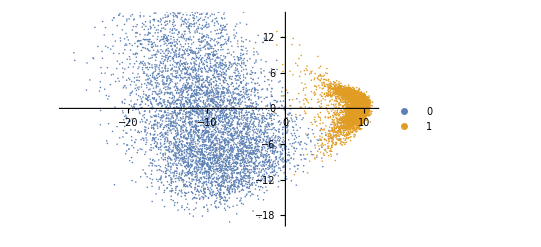

```mathematica
ListPlot[Values[projMNIST01],PlotLegends->Keys[projMNIST01]]
```

That’s all well and good, but it could be that we have just trained our model to understand the images in the training dataset we used. What if we were to throw a new, previously unseen image at it? The MNIST dataset is separated into training and testing datasets for exactly this purpose. Let’s load the test data and see how that fares

```mathematica
MNISTtest=ExampleData[{"MachineLearning","MNIST"},"TestData"];
```

```mathematica
MNISTtest//Length
```

10000

```mathematica
MNISTtestbynumber=GroupBy[MNISTtest,Last->First];
```

```mathematica
MNISTtest01=Flatten[Values[MNISTtestbynumber[[1;;2]]]];
MNISTtest01//Length
```

2115

```mathematica
projMNISTtest01=Map[dMNIST01[Flatten[ImageData[#]]]&,MNISTtestbynumber[[1;;2]],{2}];
```

If we now visualise all of those samples on our two-dimensional space, we can quite clearly distinguish between zeros and ones:

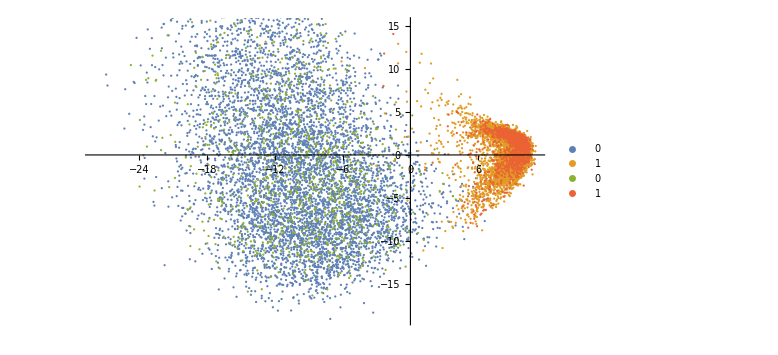

```mathematica
ListPlot[Join[Values[projMNIST01],Values[projMNISTtest01]],PlotLegends->Join[Keys[projMNIST01],Keys[projMNISTtest01]],ImageSize->Large]
```

We can also reconstruct what our model thinks a zero and a one look like:

```mathematica
Row[{Image[Partition[dMNIST01[{-10,0},"OriginalData"],28],ImageSize->Medium],Image[Partition[dMNIST01[{10,0},"OriginalData"],28],ImageSize->Medium]}]
```

-Graphics--Graphics-

And we can even use it to fill in missing data, as we did in the iris case:

```mathematica
vectormissing=MNIST01data[[1]];
vectormissing[[309;;364]]=Missing[];
imagemissing = Image[Partition[Replace[vectormissing, _Missing-> 1,{1}],28],ImageSize->Medium];
imageimputed=Image[Partition[dMNIST01[vectormissing, "ImputedVectors", PerformanceGoal->"Quality"],28],ImageSize->Medium];
```

```mathematica
Row[{Show[MNIST01[[1]],ImageSize->Medium],imagemissing,imageimputed}]
```

-Graphics--Graphics--Graphics-